#### Nicholson and Bailey

```mathematica
With[{ q = 0.5},
sol=NDSolve[
{h'[t]== h[t] * E^(-a * p[t])* R,
p'[t]== h[t]* (1- E^(-a * p[t]))* q,
h[0]== 500, p[0]==2},{h[t],p[t]},{t,0,100}];
avec = Table[x,{x,0.1,1,1}];
Rvec = Table[x,{x,0.1,100,10}];
tsol =ParallelTable[
pz = Flatten[Last[Table[Evaluate[{h[t],p[t]}/.sol],{t,0,100}]]];
{{a,R,pz[[1]]},{a,R,pz[[2]]}},
{a,avec},{R,Rvec}];
]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

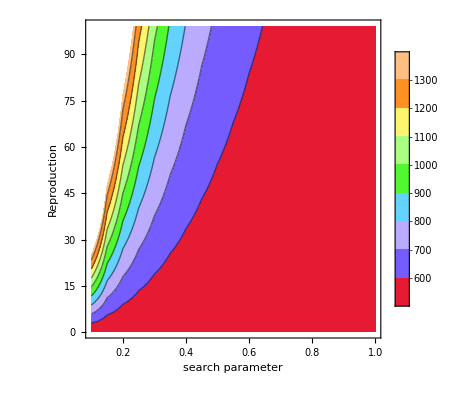

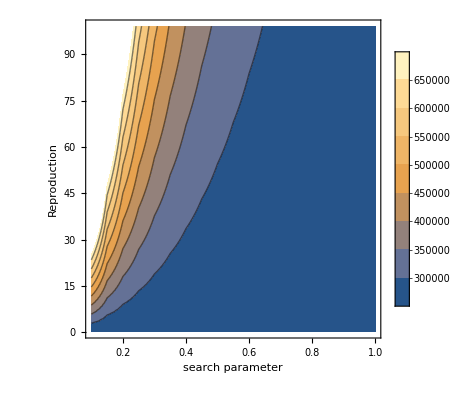

```mathematica
aRhost = ListContourPlot[Flatten[tsol,1][[All,1]],PlotLegends->Automatic,FrameLabel->{"search parameter","Reproduction"}, ColorFunction->"BrightBands"]
aRparasite =ListContourPlot[Flatten[tsol,1][[All,2]],PlotLegends->Automatic, FrameLabel->{"search parameter ","Reproduction"}]
```

#### Rogers

```mathematica
With[{ q = 0.5, Fmax = 2},
sol=NDSolve[
{h'[t]== h[t] * E^((-a * p[t]*Fmax)/( Fmax + a*h[t]))* R,
p'[t]== h[t]* (1- E^((-a * p[t]*Fmax)/( Fmax + a*h[t])))* q,
h[0]== 500, p[0]==2},{h[t],p[t]},{t,0,100}];
avec = Table[x,{x,0.1,1,0.1}];
Rvec = Table[x,{x,0.1,10,1}];
tsol =ParallelTable[
pz = Flatten[Last[Table[Evaluate[{h[t],p[t]}/.sol],{t,0,100}]]];
{{a,R,pz[[1]]},{a,R,pz[[2]]}},
{a,avec},{R,Rvec}];
]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ListContourPlot::prng: Value of option PlotRange -> {{0.1,1.},{0.1,9.1},{0,7.43852077908527×10^354}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

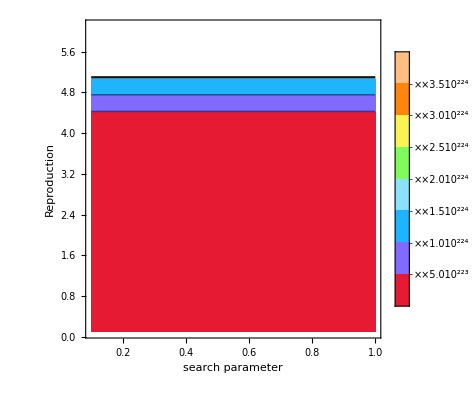

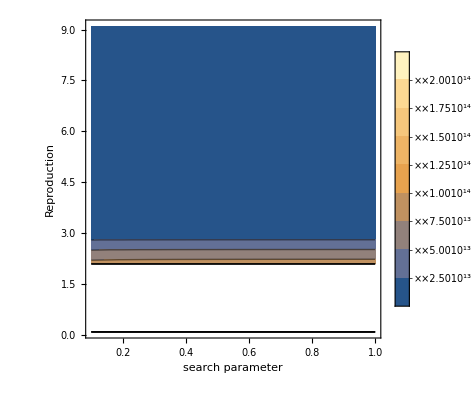

```mathematica
aRhost = ListContourPlot[Flatten[tsol,1][[All,1]],PlotLegends->Automatic,FrameLabel->{"search parameter","Reproduction"}, ColorFunction->"BrightBands"]
aRparasite =ListContourPlot[Flatten[tsol,1][[All,2]],PlotLegends->Automatic, FrameLabel->{"search parameter ","Reproduction"}]
```

#### My modification - Based Lehmann and Harlan 2019

```mathematica
With[{ q = 0.5, Fmax = 2, alpha = 0.5, z = 50, zbar = 30},
sol=NDSolve[
{h'[t]== h[t] * E^(-(((E^-(z/h[t]))*p[t]*Fmax)/(Fmax+ ((E^-(z/h[t]))*h[t]))))* (rmin + ((rmax-rmin)/(1+E^((alpha/h[t])*(z-zbar))))),
p'[t]== h[t]* (1- E^(-(((E^-(z/h[t]))*p[t]*Fmax)/(Fmax+ ((E^-(z/h[t]))*h[t])))))* q,
h[0]== 500, p[0]==2},{h[t],p[t]},{t,0,100}];
rminvec = Table[x,{x,0.1,10,1}];
rmaxvec = Table[x,{x,0.1,10,1}];
tsol =ParallelTable[
pz = Flatten[Last[Table[Evaluate[{h[t],p[t]}/.sol],{t,0,100}]]];
{{rmin,rmax,pz[[1]]},{rmin,rmax,pz[[2]]}},
{rmin,rminvec},{rmax,rmaxvec}];
]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

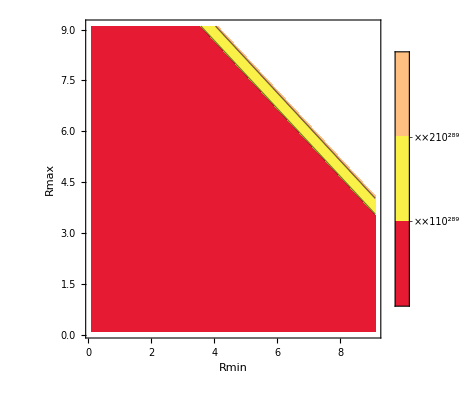

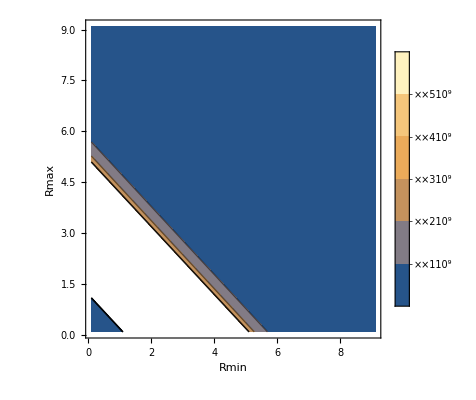

```mathematica
aRhost = ListContourPlot[Flatten[tsol,1][[All,1]],PlotLegends->Automatic,FrameLabel->{"Rmin","Rmax"}, ColorFunction->"BrightBands"]
aRparasite =ListContourPlot[Flatten[tsol,1][[All,2]],PlotLegends->Automatic, FrameLabel->{"Rmin ","Rmax"}]
```

#### Analytical Solution

```mathematica
eqns={h'[t]== h[t] * E^(-a * p[t])* R,
p'[t]== h[t]* (1- E^(-a * p[t]))* q,h[0]== 5000,p[0]==2};
sol=DSolve[eqns,{h,p},t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{}

```mathematica
Plot[{h[t]/.sol,p[t]/.sol},{t,0,100}]
```

#### New plots hosts/ parasites vs time - Nicholson and Bailey

```mathematica
Manipulate[sol=NDSolve[
{h'[t]== (h[t] * E^(-a * p[t])* R)-h[t],
p'[t]== (h[t]* (1- E^(-a * p[t]))* q)-p[t],
h[0]== 1000, p[0]==5},{h[t],p[t]},{t,0,100}];
GraphicsGrid[{{Plot[Evaluate[{h[t]/.sol},{t,0,100},  AxesLabel->Automatic ,PlotRange -> Full,  PlotLabel-> "Host - Nich-Bail"]], Plot[Evaluate[{p[t]/.sol},{t,0,100}, AxesLabel->Automatic ,PlotRange -> Full, PlotLabel-> "Par-Nich-Bail"]]}}],
{{R,10,"reproduction"},1,1000,10,Appearance->"Labeled"}, 
{{a,0.5,"search parameter"},0.1,1,0.1,Appearance->"Labeled"},
{{q,0.5,"females"},0.1,1,0.1,Appearance->"Labeled"}
]
```

#### New plots hosts/ parasites vs time - Rogers

```mathematica
Manipulate[sol=NDSolve[
{h'[t]== (h[t] * E^((-a * p[t]*Fmax)/( Fmax + a*h[t]))* R)-h[t],
p'[t]== (h[t]* (1- E^((-a * p[t]*Fmax)/( Fmax + a*h[t])))* q) - p[t],
h[0]== 1000, p[0]==5},{h[t],p[t]},{t,0,100}];
GraphicsGrid[{{Plot[Evaluate[{h[t]/.sol},{t,0,100},  AxesLabel->Automatic ,PlotRange -> Full,  PlotLabel-> "Host - Roger"]], Plot[Evaluate[{p[t]/.sol},{t,0,100},  AxesLabel->Automatic ,PlotRange -> Full, PlotLabel-> "Par-Roger"]]}}],
{{R,5,"reproduction"},1,100,10,Appearance->"Labeled"}, 
{{a,0.5,"search parameter"},0.1,1,0.1,Appearance->"Labeled"},
{{q,0.5,"females"},0.1,1,0.1,Appearance->"Labeled"},
{{Fmax,10,"max parasite progeny"},1,100,1,Appearance->"Labeled"}
]
```

#### New plots hosts/ parasites vs time - My mod -Based Lehmann and Harlan 2019

```mathematica
Manipulate[sol=NDSolve[
{h'[t]== (h[t] * E^(-(((E^-(z/h[t]))*p[t]*Fmax)/(Fmax+ ((E^-(z/h[t]))*h[t]))))* (rmin + ((rmax-rmin)/(1+E^((alpha/h[t])*(z-zbar[t]))))))-h[t],
p'[t]== (h[t]* (1- E^(-(((E^-(z/h[t]))*p[t]*Fmax)/(Fmax+ ((E^-(z/h[t]))*h[t])))))* q)-p[t],
zbar'[t] == sigmag^2 (-(alpha ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])+(alpha (z-zbar[t]))/h[t]) (rmax-rmin))/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^2 h[t])+ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])) ((rmax-rmin)/(1+ⅇ^((alpha (z-zbar[t]))/h[t]))+rmin) ((ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t]))-1/2 sigma^2 (-(6 alpha^3 ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])+(3 alpha (z-zbar[t]))/h[t]) (rmax-rmin))/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^4 h[t]^3)+(2 alpha^2 ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])+(2 alpha (z-zbar[t]))/h[t]) (rmax-rmin) ((ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])))/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^3 h[t]^2)-(alpha ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])+(alpha (z-zbar[t]))/h[t]) (rmax-rmin) ((ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t]))^2)/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^2 h[t])+ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])) ((rmax-rmin)/(1+ⅇ^((alpha (z-zbar[t]))/h[t]))+rmin) ((ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t]))^3+1/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^3 h[t]^2)2 alpha^2 ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])+(2 alpha (z-zbar[t]))/h[t]) (rmax-rmin) (alpha/h[t]+(ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t]))-1/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^2 h[t])alpha ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])+(alpha (z-zbar[t]))/h[t]) (rmax-rmin) ((ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])) (alpha/h[t]+(ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t]))-1/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^2 h[t])alpha ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])+(alpha (z-zbar[t]))/h[t]) (rmax-rmin) (alpha/h[t]+(ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t]))^2+1/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^3 h[t]^2)2 alpha^2 ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])+(2 alpha (z-zbar[t]))/h[t]) (rmax-rmin) ((2 alpha)/h[t]+(ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t]))-1/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^2 h[t])3 alpha ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])+(alpha (z-zbar[t]))/h[t]) (rmax-rmin) (-(2 ⅇ^(-(3 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z))^2 h[t]^2 p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^3)+(ⅇ^(-(2 z)/(1+z)) Fmax (-(2 z)/(1+z)^3+2/(1+z)^2) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)+(ⅇ^(-(2 z)/(1+z)) Fmax ((2 z)/(1+z)^2-2/(1+z)) (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)+(ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z))^2 h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (-(2 z)/(1+z)^3+2/(1+z)^2) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z))^2 p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t]))+3 ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])) ((rmax-rmin)/(1+ⅇ^((alpha (z-zbar[t]))/h[t]))+rmin) ((ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])) (-(2 ⅇ^(-(3 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z))^2 h[t]^2 p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^3)+(ⅇ^(-(2 z)/(1+z)) Fmax (-(2 z)/(1+z)^3+2/(1+z)^2) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)+(ⅇ^(-(2 z)/(1+z)) Fmax ((2 z)/(1+z)^2-2/(1+z)) (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)+(ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z))^2 h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (-(2 z)/(1+z)^3+2/(1+z)^2) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z))^2 p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t]))+ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])) ((rmax-rmin)/(1+ⅇ^((alpha (z-zbar[t]))/h[t]))+rmin) ((6 ⅇ^(-(4 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z))^3 h[t]^3 p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^4)-(6 ⅇ^(-(3 z)/(1+z)) Fmax (-(2 z)/(1+z)^3+2/(1+z)^2) (z/(1+z)^2-1/(1+z)) h[t]^2 p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^3)-(2 ⅇ^(-(3 z)/(1+z)) Fmax ((3 z)/(1+z)^2-3/(1+z)) (z/(1+z)^2-1/(1+z))^2 h[t]^2 p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^3)-(2 ⅇ^(-(3 z)/(1+z)) Fmax ((2 z)/(1+z)^2-2/(1+z)) (z/(1+z)^2-1/(1+z))^2 h[t]^2 p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^3)-(2 ⅇ^(-(3 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z))^3 h[t]^2 p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^3)+(ⅇ^(-(2 z)/(1+z)) Fmax ((6 z)/(1+z)^4-6/(1+z)^3) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)+(2 ⅇ^(-(2 z)/(1+z)) Fmax (-(2 z)/(1+z)^3+2/(1+z)^2) ((2 z)/(1+z)^2-2/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)+(3 ⅇ^(-(2 z)/(1+z)) Fmax (-(2 z)/(1+z)^3+2/(1+z)^2) (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)+(ⅇ^(-(2 z)/(1+z)) Fmax (-(4 z)/(1+z)^3+4/(1+z)^2) (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)+(ⅇ^(-(2 z)/(1+z)) Fmax ((2 z)/(1+z)^2-2/(1+z))^2 (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)+(ⅇ^(-(2 z)/(1+z)) Fmax ((2 z)/(1+z)^2-2/(1+z)) (z/(1+z)^2-1/(1+z))^2 h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)+(ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z))^3 h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax ((6 z)/(1+z)^4-6/(1+z)^3) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])-(3 ⅇ^(-z/(1+z)) Fmax (-(2 z)/(1+z)^3+2/(1+z)^2) (z/(1+z)^2-1/(1+z)) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z))^3 p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])))),
h[0]== 1000, p[0]==5, zbar[0]==30},{h[t],p[t],zbar[t]},{t,0,100}];
GraphicsGrid[{{Plot[Evaluate[{h[t]/.sol},{t,0,100}, AxesLabel->Automatic ,PlotRange -> Full,  PlotLabel-> "Host - my mod"]], Plot[Evaluate[{p[t]/.sol},{t,0,100},  AxesLabel->Automatic ,PlotRange -> Full, PlotLabel-> "Par-my mod"]],Plot[Evaluate[{zbar[t]/.sol},{t,0,100}, AxesLabel->Automatic ,PlotRange -> {{0,100},{0,100}}, PlotLabel-> "mean syllable rate-my mod"]]}}],
{{rmin,2,"reproduction min"},1,100,10,Appearance->"Labeled"}, 
{{rmax,8,"reproduction max"},1,100,10,Appearance->"Labeled"}, 
{{alpha,0.5,"slope"},0.1,1,0.1,Appearance->"Labeled"},
{{q,0.5,"females prop"},0.1,1,0.1,Appearance->"Labeled"},
{{Fmax,10,"max parasite progeny"},1,100,1,Appearance->"Labeled"},
{{z,50,"Syllable rate - ambient"},1,100,1,Appearance->"Labeled"},
{{sigmag,1,"genetic Var"},0.1,1,0.1,Appearance->"Labeled"},
{{sigma,1,"phenotypic Var"},0.1,1,0.1,Appearance->"Labeled"}
]
```

NDSolve::ndode: The equations {50[0]==30} are not differential equations or initial conditions in the dependent variables {h,p}.

ReplaceAll::reps: {NDSolve[{h'[t]==-h[t]+ⅇ^Times[«4»] (2+Times[«2»]) h[t],p'[t]==0.5 (1+Times[«2»]) h[t]-p[t],0==-(3. ⅇ^Plus[«2»])/(Plus[«2»]^2 h[«1»])+ⅇ^Times[«4»] (2+Times[«2»]) (Times[«4»]+Times[«5»])+1/2 (Times[«4»]+Times[«4»]+Times[«5»]+Times[«5»]+Times[«5»]+Times[«5»]+Times[«4»]+Times[«5»]+Times[«6»]+Times[«5»]+Times[«5»]),h[0]==1000,p[0]==5,50[0]==30},{h[t],p[t],50[t]},{t,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{h'[0.00204286]==-h[0.00204286]+ⅇ^Times[«4»] (2+Times[«2»]) h[0.00204286],p'[0.00204286]==0.5 (1+Times[«2»]) h[0.00204286]-p[0.00204286],0==-(3. ⅇ^Plus[«2»])/(Plus[«2»]^2 h[«1»])+ⅇ^Times[«4»] (2+Times[«2»]) (Times[«4»]+Times[«5»])+1/2 (Times[«4»]+Times[«4»]+Times[«5»]+Times[«5»]+Times[«5»]+Times[«5»]+Times[«4»]+Times[«5»]+Times[«6»]+Times[«5»]+Times[«5»]),h[0]==1000,p[0]==5,50[0]==30},{h[0.00204286],p[0.00204286],50[0.00204286]},{0.00204286,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{h'[0.00204286]==-1. h[0.00204286]+2.71828^Times[«4»] (2.+Times[«2»]) h[0.00204286],p'[0.00204286]==0.5 (1.+Times[«2»]) h[0.00204286]-1. p[0.00204286],0.==-(3. 2.71828^Plus[«2»])/(Plus[«2»]^2 h[«1»])+2.71828^Times[«4»] (2.+Times[«2»]) (Times[«4»]+Times[«5»])+0.5 (Times[«4»]+Times[«4»]+Times[«5»]+Times[«5»]+Times[«5»]+Times[«5»]+Times[«4»]+Times[«5»]+Times[«6»]+Times[«5»]+Times[«5»]),h[0.]==1000.,p[0.]==5.,50.[0.]==30.},{h[0.00204286],p[«21»],50.[0.00204286]},{0.00204286,0.,100.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndode: The equations {50[0]==30} are not differential equations or initial conditions in the dependent variables {h,p}.

General::stop: Further output of NDSolve::ndode will be suppressed during this calculation.

NDSolve::ndode: The equations {50[0]==30} are not differential equations or initial conditions in the dependent variables {h,p}.

ReplaceAll::reps: {NDSolve[{h'[t]==-h[t]+ⅇ^Times[«4»] (2+Times[«2»]) h[t],p'[t]==0.5 (1+Times[«2»]) h[t]-p[t],0==-(3. ⅇ^Plus[«2»])/(Plus[«2»]^2 h[«1»])+ⅇ^Times[«4»] (2+Times[«2»]) (Times[«4»]+Times[«5»])+1/2 (Times[«4»]+Times[«4»]+Times[«5»]+Times[«5»]+Times[«5»]+Times[«5»]+Times[«4»]+Times[«5»]+Times[«6»]+Times[«5»]+Times[«5»]),h[0]==1000,p[0]==5,50[0]==30},{h[t],p[t],50[t]},{t,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{h'[0.00204286]==-h[0.00204286]+ⅇ^Times[«4»] (2+Times[«2»]) h[0.00204286],p'[0.00204286]==0.5 (1+Times[«2»]) h[0.00204286]-p[0.00204286],0==-(3. ⅇ^Plus[«2»])/(Plus[«2»]^2 h[«1»])+ⅇ^Times[«4»] (2+Times[«2»]) (Times[«4»]+Times[«5»])+1/2 (Times[«4»]+Times[«4»]+Times[«5»]+Times[«5»]+Times[«5»]+Times[«5»]+Times[«4»]+Times[«5»]+Times[«6»]+Times[«5»]+Times[«5»]),h[0]==1000,p[0]==5,50[0]==30},{h[0.00204286],p[0.00204286],50[0.00204286]},{0.00204286,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{h'[0.00204286]==-1. h[0.00204286]+2.71828^Times[«4»] (2.+Times[«2»]) h[0.00204286],p'[0.00204286]==0.5 (1.+Times[«2»]) h[0.00204286]-1. p[0.00204286],0.==-(3. 2.71828^Plus[«2»])/(Plus[«2»]^2 h[«1»])+2.71828^Times[«4»] (2.+Times[«2»]) (Times[«4»]+Times[«5»])+0.5 (Times[«4»]+Times[«4»]+Times[«5»]+Times[«5»]+Times[«5»]+Times[«5»]+Times[«4»]+Times[«5»]+Times[«6»]+Times[«5»]+Times[«5»]),h[0.]==1000.,p[0.]==5.,50.[0.]==30.},{h[0.00204286],p[«21»],50.[0.00204286]},{0.00204286,0.,100.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ndode: The equations {50[0]==30} are not differential equations or initial conditions in the dependent variables {h,p}.

General::stop: Further output of NDSolve::ndode will be suppressed during this calculation.

```mathematica
With[{rmax=2,rmin=0.01,sigma=1,alpha = 0.5, z = 90, Fmax =3, sigmag =1},
sol=NDSolve[
{h'[t]== (h[t] * E^(-(((E^-(z/(1+z)))*p[t]*Fmax)/(Fmax+ ((E^-(z/(1+z)))*h[t]))))* (rmin + ((rmax-rmin)/(1+E^((alpha/h[t])*(z-zbar[t]))))))-h[t],
p'[t]== (h[t]* (1- E^(-(((E^- (z/(1+z)))*p[t]*Fmax)/(Fmax+ ((E^- (z/(1+z)))*h[t])))))* q)- p[t],
zbar'[t] == sigmag^2 (-(alpha ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])+(alpha (z-zbar[t]))/h[t]) (rmax-rmin))/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^2 h[t])+ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])) ((rmax-rmin)/(1+ⅇ^((alpha (z-zbar[t]))/h[t]))+rmin) ((ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t]))-1/2 sigma^2 (-(6 alpha^3 ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])+(3 alpha (z-zbar[t]))/h[t]) (rmax-rmin))/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^4 h[t]^3)+(2 alpha^2 ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])+(2 alpha (z-zbar[t]))/h[t]) (rmax-rmin) ((ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])))/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^3 h[t]^2)-(alpha ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])+(alpha (z-zbar[t]))/h[t]) (rmax-rmin) ((ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t]))^2)/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^2 h[t])+ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])) ((rmax-rmin)/(1+ⅇ^((alpha (z-zbar[t]))/h[t]))+rmin) ((ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t]))^3+1/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^3 h[t]^2)2 alpha^2 ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])+(2 alpha (z-zbar[t]))/h[t]) (rmax-rmin) (alpha/h[t]+(ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t]))-1/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^2 h[t])alpha ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])+(alpha (z-zbar[t]))/h[t]) (rmax-rmin) ((ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])) (alpha/h[t]+(ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t]))-1/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^2 h[t])alpha ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])+(alpha (z-zbar[t]))/h[t]) (rmax-rmin) (alpha/h[t]+(ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t]))^2+1/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^3 h[t]^2)2 alpha^2 ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])+(2 alpha (z-zbar[t]))/h[t]) (rmax-rmin) ((2 alpha)/h[t]+(ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t]))-1/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^2 h[t])3 alpha ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])+(alpha (z-zbar[t]))/h[t]) (rmax-rmin) (-(2 ⅇ^(-(3 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z))^2 h[t]^2 p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^3)+(ⅇ^(-(2 z)/(1+z)) Fmax (-(2 z)/(1+z)^3+2/(1+z)^2) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)+(ⅇ^(-(2 z)/(1+z)) Fmax ((2 z)/(1+z)^2-2/(1+z)) (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)+(ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z))^2 h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (-(2 z)/(1+z)^3+2/(1+z)^2) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z))^2 p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t]))+3 ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])) ((rmax-rmin)/(1+ⅇ^((alpha (z-zbar[t]))/h[t]))+rmin) ((ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z)) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])) (-(2 ⅇ^(-(3 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z))^2 h[t]^2 p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^3)+(ⅇ^(-(2 z)/(1+z)) Fmax (-(2 z)/(1+z)^3+2/(1+z)^2) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)+(ⅇ^(-(2 z)/(1+z)) Fmax ((2 z)/(1+z)^2-2/(1+z)) (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)+(ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z))^2 h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax (-(2 z)/(1+z)^3+2/(1+z)^2) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z))^2 p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t]))+ⅇ^(-(ⅇ^(-z/(1+z)) Fmax p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])) ((rmax-rmin)/(1+ⅇ^((alpha (z-zbar[t]))/h[t]))+rmin) ((6 ⅇ^(-(4 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z))^3 h[t]^3 p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^4)-(6 ⅇ^(-(3 z)/(1+z)) Fmax (-(2 z)/(1+z)^3+2/(1+z)^2) (z/(1+z)^2-1/(1+z)) h[t]^2 p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^3)-(2 ⅇ^(-(3 z)/(1+z)) Fmax ((3 z)/(1+z)^2-3/(1+z)) (z/(1+z)^2-1/(1+z))^2 h[t]^2 p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^3)-(2 ⅇ^(-(3 z)/(1+z)) Fmax ((2 z)/(1+z)^2-2/(1+z)) (z/(1+z)^2-1/(1+z))^2 h[t]^2 p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^3)-(2 ⅇ^(-(3 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z))^3 h[t]^2 p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^3)+(ⅇ^(-(2 z)/(1+z)) Fmax ((6 z)/(1+z)^4-6/(1+z)^3) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)+(2 ⅇ^(-(2 z)/(1+z)) Fmax (-(2 z)/(1+z)^3+2/(1+z)^2) ((2 z)/(1+z)^2-2/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)+(3 ⅇ^(-(2 z)/(1+z)) Fmax (-(2 z)/(1+z)^3+2/(1+z)^2) (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)+(ⅇ^(-(2 z)/(1+z)) Fmax (-(4 z)/(1+z)^3+4/(1+z)^2) (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)+(ⅇ^(-(2 z)/(1+z)) Fmax ((2 z)/(1+z)^2-2/(1+z))^2 (z/(1+z)^2-1/(1+z)) h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)+(ⅇ^(-(2 z)/(1+z)) Fmax ((2 z)/(1+z)^2-2/(1+z)) (z/(1+z)^2-1/(1+z))^2 h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)+(ⅇ^(-(2 z)/(1+z)) Fmax (z/(1+z)^2-1/(1+z))^3 h[t] p[t])/((Fmax+ⅇ^(-z/(1+z)) h[t])^2)-(ⅇ^(-z/(1+z)) Fmax ((6 z)/(1+z)^4-6/(1+z)^3) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])-(3 ⅇ^(-z/(1+z)) Fmax (-(2 z)/(1+z)^3+2/(1+z)^2) (z/(1+z)^2-1/(1+z)) p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])-(ⅇ^(-z/(1+z)) Fmax (z/(1+z)^2-1/(1+z))^3 p[t])/(Fmax+ⅇ^(-z/(1+z)) h[t])))),
h[0]== 500, p[0]==200, zbar[0]==90},{h[t],p[t],zbar[t]},{t,0,100}];

qvec = Table[xx,{xx,0.01,1,0.1}];
tsol =ParallelTable[Flatten[Last[Table[Evaluate[{h[t],p[t],zbar[t]}/.sol],{t,0,100}]]],{q,qvec}];
zqplot = GraphicsGrid[{{
ListPlot[Transpose[{qvec,tsol[[All,1]]}],Frame->True,PlotRange->Full,FrameLabel->{"females prop","Steady state of host Pop."}],
ListPlot[Transpose[{qvec,tsol[[All,2]]}],Frame->True,PlotRange->Full,FrameLabel->{"females prop","Steady state of parasite"}],
ListPlot[Transpose[{qvec,tsol[[All,3]]}],Frame->True,PlotRange -> {{0,1},{0,100}},FrameLabel->{"females prop","mean syllable rate"}]

}},ImageSize->Large]
]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::ndsz: At t == 24.9251, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 26.2958, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {27} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {27} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {27} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

NDSolve::nlnum: The function value {2.71684×10^-9,1.38508×10^-14,Indeterminate} is not a list of numbers with dimensions {3} at {t,h[t],p[t],zbar[t]} = {41.0964,-2.74428×10^-9,-1.38508×10^-14,1.23404×10^11}.

-Graphics-

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

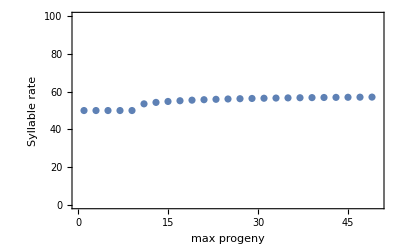

```mathematica
With[{rmax=8,rmin=2,sigma=1,alpha = 0.5, z = 30,q = 0.5, sigmag =1},
sol=NDSolve[
{h'[t]== (h[t] * E^(-(((E^-(z/h[t]))*p[t]*Fmax)/(Fmax+ ((E^-(z/h[t]))*h[t]))))* (rmin + ((rmax-rmin)/(1+E^((alpha/h[t])*(z-zbar[t]))))))-h[t],
p'[t]== (h[t]* (1- E^(-(((E^-(z/h[t]))*p[t]*Fmax)/(Fmax+ ((E^-(z/h[t]))*h[t])))))* q) -p[t],
zbar'[t] == sigmag^2 (-((alpha ⅇ^(-(ⅇ^(-z/h[t]) Fmax p[t])/(Fmax+ⅇ^(-z/h[t]) h[t])+(alpha (z-zbar[t]))/h[t]) (rmax-rmin))/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^2 h[t]))+ⅇ^(-(ⅇ^(-z/h[t]) Fmax p[t])/(Fmax+ⅇ^(-z/h[t]) h[t])) ((rmax-rmin)/(1+ⅇ^((alpha (z-zbar[t]))/h[t]))+rmin) (-(ⅇ^(-(2 z)/h[t]) Fmax p[t])/((Fmax+ⅇ^(-z/h[t]) h[t])^2)+(ⅇ^(-z/h[t]) Fmax p[t])/(h[t] (Fmax+ⅇ^(-z/h[t]) h[t])))-1/2 sigma^2 (-((6 alpha^3 ⅇ^(-(ⅇ^(-z/h[t]) Fmax p[t])/(Fmax+ⅇ^(-z/h[t]) h[t])+(3 alpha (z-zbar[t]))/h[t]) (rmax-rmin))/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^4 h[t]^3))+ⅇ^(-(ⅇ^(-z/h[t]) Fmax p[t])/(Fmax+ⅇ^(-z/h[t]) h[t])) ((rmax-rmin)/(1+ⅇ^((alpha (z-zbar[t]))/h[t]))+rmin) (-(6 ⅇ^(-(4 z)/h[t]) Fmax p[t])/((Fmax+ⅇ^(-z/h[t]) h[t])^4)+(12 ⅇ^(-(3 z)/h[t]) Fmax p[t])/(h[t] (Fmax+ⅇ^(-z/h[t]) h[t])^3)-(7 ⅇ^(-(2 z)/h[t]) Fmax p[t])/(h[t]^2 (Fmax+ⅇ^(-z/h[t]) h[t])^2)+(ⅇ^(-z/h[t]) Fmax p[t])/(h[t]^3 (Fmax+ⅇ^(-z/h[t]) h[t])))-1/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^2 h[t])3 alpha ⅇ^(-(ⅇ^(-z/h[t]) Fmax p[t])/(Fmax+ⅇ^(-z/h[t]) h[t])+(alpha (z-zbar[t]))/h[t]) (rmax-rmin) (-(2 ⅇ^(-(3 z)/h[t]) Fmax p[t])/((Fmax+ⅇ^(-z/h[t]) h[t])^3)+(3 ⅇ^(-(2 z)/h[t]) Fmax p[t])/(h[t] (Fmax+ⅇ^(-z/h[t]) h[t])^2)-(ⅇ^(-z/h[t]) Fmax p[t])/(h[t]^2 (Fmax+ⅇ^(-z/h[t]) h[t])))+(2 alpha^2 ⅇ^(-(ⅇ^(-z/h[t]) Fmax p[t])/(Fmax+ⅇ^(-z/h[t]) h[t])+(2 alpha (z-zbar[t]))/h[t]) (rmax-rmin) (-(ⅇ^(-(2 z)/h[t]) Fmax p[t])/((Fmax+ⅇ^(-z/h[t]) h[t])^2)+(ⅇ^(-z/h[t]) Fmax p[t])/(h[t] (Fmax+ⅇ^(-z/h[t]) h[t]))))/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^3 h[t]^2)+3 ⅇ^(-(ⅇ^(-z/h[t]) Fmax p[t])/(Fmax+ⅇ^(-z/h[t]) h[t])) ((rmax-rmin)/(1+ⅇ^((alpha (z-zbar[t]))/h[t]))+rmin) (-(2 ⅇ^(-(3 z)/h[t]) Fmax p[t])/((Fmax+ⅇ^(-z/h[t]) h[t])^3)+(3 ⅇ^(-(2 z)/h[t]) Fmax p[t])/(h[t] (Fmax+ⅇ^(-z/h[t]) h[t])^2)-(ⅇ^(-z/h[t]) Fmax p[t])/(h[t]^2 (Fmax+ⅇ^(-z/h[t]) h[t]))) (-(ⅇ^(-(2 z)/h[t]) Fmax p[t])/((Fmax+ⅇ^(-z/h[t]) h[t])^2)+(ⅇ^(-z/h[t]) Fmax p[t])/(h[t] (Fmax+ⅇ^(-z/h[t]) h[t])))-(alpha ⅇ^(-(ⅇ^(-z/h[t]) Fmax p[t])/(Fmax+ⅇ^(-z/h[t]) h[t])+(alpha (z-zbar[t]))/h[t]) (rmax-rmin) (-(ⅇ^(-(2 z)/h[t]) Fmax p[t])/((Fmax+ⅇ^(-z/h[t]) h[t])^2)+(ⅇ^(-z/h[t]) Fmax p[t])/(h[t] (Fmax+ⅇ^(-z/h[t]) h[t])))^2)/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^2 h[t])+ⅇ^(-(ⅇ^(-z/h[t]) Fmax p[t])/(Fmax+ⅇ^(-z/h[t]) h[t])) ((rmax-rmin)/(1+ⅇ^((alpha (z-zbar[t]))/h[t]))+rmin) (-(ⅇ^(-(2 z)/h[t]) Fmax p[t])/((Fmax+ⅇ^(-z/h[t]) h[t])^2)+(ⅇ^(-z/h[t]) Fmax p[t])/(h[t] (Fmax+ⅇ^(-z/h[t]) h[t])))^3+(2 alpha^2 ⅇ^(-(ⅇ^(-z/h[t]) Fmax p[t])/(Fmax+ⅇ^(-z/h[t]) h[t])+(2 alpha (z-zbar[t]))/h[t]) (rmax-rmin) (alpha/h[t]-(ⅇ^(-(2 z)/h[t]) Fmax p[t])/((Fmax+ⅇ^(-z/h[t]) h[t])^2)+(ⅇ^(-z/h[t]) Fmax p[t])/(h[t] (Fmax+ⅇ^(-z/h[t]) h[t]))))/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^3 h[t]^2)-1/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^2 h[t])alpha ⅇ^(-(ⅇ^(-z/h[t]) Fmax p[t])/(Fmax+ⅇ^(-z/h[t]) h[t])+(alpha (z-zbar[t]))/h[t]) (rmax-rmin) (-(ⅇ^(-(2 z)/h[t]) Fmax p[t])/((Fmax+ⅇ^(-z/h[t]) h[t])^2)+(ⅇ^(-z/h[t]) Fmax p[t])/(h[t] (Fmax+ⅇ^(-z/h[t]) h[t]))) (alpha/h[t]-(ⅇ^(-(2 z)/h[t]) Fmax p[t])/((Fmax+ⅇ^(-z/h[t]) h[t])^2)+(ⅇ^(-z/h[t]) Fmax p[t])/(h[t] (Fmax+ⅇ^(-z/h[t]) h[t])))-(alpha ⅇ^(-(ⅇ^(-z/h[t]) Fmax p[t])/(Fmax+ⅇ^(-z/h[t]) h[t])+(alpha (z-zbar[t]))/h[t]) (rmax-rmin) (alpha/h[t]-(ⅇ^(-(2 z)/h[t]) Fmax p[t])/((Fmax+ⅇ^(-z/h[t]) h[t])^2)+(ⅇ^(-z/h[t]) Fmax p[t])/(h[t] (Fmax+ⅇ^(-z/h[t]) h[t])))^2)/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^2 h[t])+(2 alpha^2 ⅇ^(-(ⅇ^(-z/h[t]) Fmax p[t])/(Fmax+ⅇ^(-z/h[t]) h[t])+(2 alpha (z-zbar[t]))/h[t]) (rmax-rmin) ((2 alpha)/h[t]-(ⅇ^(-(2 z)/h[t]) Fmax p[t])/((Fmax+ⅇ^(-z/h[t]) h[t])^2)+(ⅇ^(-z/h[t]) Fmax p[t])/(h[t] (Fmax+ⅇ^(-z/h[t]) h[t]))))/((1+ⅇ^((alpha (z-zbar[t]))/h[t]))^3 h[t]^2))),
h[0]== 1000, p[0]==5, zbar[0]==50},{h[t],p[t],zbar[t]},{t,0,100}];

Fmaxvec = Table[xx,{xx,1,50,2}];
tsol =ParallelTable[Flatten[Last[Table[Evaluate[{h[t],p[t],zbar[t]}/.sol],{t,1,100}]]],{Fmax,Fmaxvec}];
zqplot = GraphicsGrid[{{
ListPlot[Transpose[{Fmaxvec,tsol[[All,1]]}],Frame->True,PlotRange->Full, FrameLabel->{"max progeny","Steady state of host Pop."}],
ListPlot[Transpose[{Fmaxvec,tsol[[All,2]]}],Frame->True,PlotRange->Full,FrameLabel->{"max progeny","Steady state of parasite"}],
ListPlot[Transpose[{Fmaxvec,tsol[[All,3]]}],Frame->True,PlotRange->{{0,50},{0,100}},FrameLabel->{"max progeny","Syllable rate"}]

}},ImageSize->Large]
]
```

```mathematica
r =rmin + ((rmax -rmin)/(1 + E^(-beta * (z -zbar))))
```

(rmax-rmin)/(1+ⅇ^(-beta (z-zbar)))+rmin

```mathematica
r
```

(rmax-rmin)/(1+ⅇ^(-beta (z-zbar)))+rmin

```mathematica
host = H * E^((r* (1-(H/k)))-((E^(-z/H)*P*Fmax)/(Fmax +E^(-z/H)*H)))
```

ⅇ^(-(ⅇ^(-z/H) Fmax P)/(Fmax+ⅇ^(-z/H) H)+(1-H/k) r) H

```mathematica
parst = H*(1-E^(E^(-z/H)*P*Fmax)/(Fmax +E^(-z/H)*H))*q
```

H (1-(ⅇ^(ⅇ^(-z/H) Fmax P))/(Fmax+ⅇ^(-z/H) H)) q

```mathematica
sol1 =Solve[{(H * E^(((rmin + ((rmax -rmin)/(1 + E^(-beta * (z -zbar)))))* (1-(H/k)))-((E^(z/H)*P*Fmax)/(Fmax +E^(z/H)*H))))-H==0,(H*(1-E^(E^(z/H)*P*Fmax)/(Fmax +E^(z/H)*H))*q)-P==0},{H,P}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{-H+ⅇ^(-(ⅇ^(z/H) Fmax P)/(Fmax+ⅇ^(z/H) H)+(1-H/k) ((rmax-rmin)/(1+ⅇ^(-beta (z-zbar)))+rmin)) H==0,-P+H (1-(ⅇ^(z/H) Fmax P)/(Fmax+ⅇ^(z/H) H)) q==0},{H,P}]

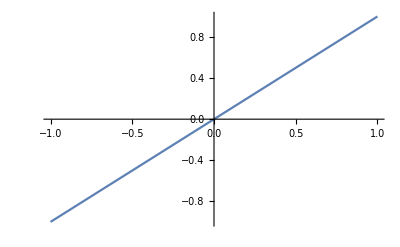

```mathematica
Plot[P/.sol1, {P,-1,1}]
```

```mathematica
Plot[H/.sol1, {H,-1,1}]
```

-Graphics-

```mathematica
With[{beta = 0.5, z = 30,q = 0.5,  Fmax =2, zbar = 50, k =1000},
sol=NDSolve[
{h'[t]== (h[t] * E^(((rmin + ((rmax -rmin)/(1 + E^(-beta * (z -zbar)))))* (1-(h[t] /k)))-((E^(-z/h[t] )*p[t]*Fmax)/(Fmax +E^(-z/h[t] )*h[t] ))))-h[t],
p'[t]==(h[t]*(1-(E^(-z/h[t])*p[t]*Fmax)/(Fmax +E^(-z/h[t])*h[t]))*q)-p[t],
h[0]== 500, p[0]==2},{h[t],p[t]},{t,0,100}];
rminvec = Table[x,{x,5,10,1}];
rmaxvec = Table[x,{x,5,10,1}];
tsol =ParallelTable[
pz = Flatten[Last[Table[Evaluate[{h[t],p[t]}/.sol],{t,0,100}]]];
{{rmin,rmax,pz[[1]]},{rmin,rmax,pz[[2]]}},
{rmin,rminvec},{rmax,rmaxvec}];
]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

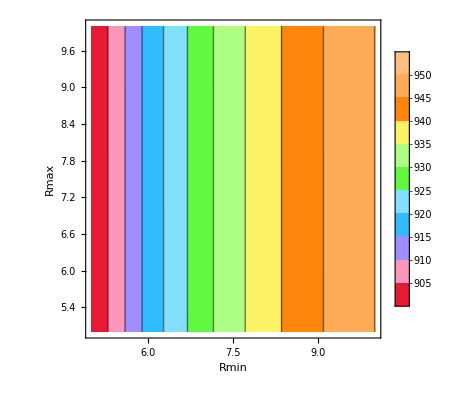

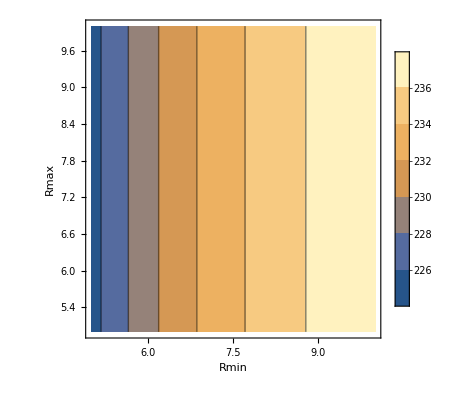

```mathematica
aRhost = ListContourPlot[Flatten[tsol,1][[All,1]],PlotLegends->Automatic,FrameLabel->{"Rmin","Rmax"}, ColorFunction->"BrightBands"]
aRparasite =ListContourPlot[Flatten[tsol,1][[All,2]],PlotLegends->Automatic, FrameLabel->{"Rmin ","Rmax"}]
```

```mathematica
H = H * E^(((rmin + ((rmax -rmin)/(1 + E^(-beta * (z -zbar)))))* (1-(H/k)))-((E^(-z/H)*P*Fmax)/(Fmax +E^(-z/H)*H)))
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ⅇ^(-(ⅇ^(-z/H) Fmax P)/(Fmax+ⅇ^Times[«1»] H)+(1-H/k) ((rmax-rmin)/(1+Power[«1»])+rmin)).

Hold[ⅇ^(-(ⅇ^(-z/H) Fmax P)/(Fmax+ⅇ^(-z/H) H)+(1-H/k) ((rmax-rmin)/(1+ⅇ^(-beta (z-zbar)))+rmin)) H]

```mathematica
rmin = 0.5; rmax =2; k = 10000; beta =0.5; Fmax =2 ; z =20;zbar =50;q=0.5;
eq1=H'[t]==(H[t] * E^(((rmin + ((rmax -rmin)/(1 + E^(-beta * (z -zbar)))))* (1-(H[t]/k)))-((E^(-z/H[t])*P[t]*Fmax)/(Fmax +E^(-z/H[t])*H[t]))))-H[t]
eq2=P'[t]==(H[t]*(1-(E^(-z/H[t])*P[t]*Fmax)/(Fmax +E^(-z/H[t])*H[t]))*q)-P[t]
sol=NDSolve[{eq1,eq2,H[0]==500,P[0]==2},{H,P},{t,0,1000}]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ⅇ^(-(ⅇ^(-z/H) Fmax P)/(Fmax+ⅇ^Times[«1»] H)+(1-H/k) ((rmax-rmin)/(1+Power[«1»])+rmin)).

Hold[eq1=H'[t]==H[t] ⅇ^((rmin+(rmax-rmin)/(1+ⅇ^(-beta (z-zbar)))) (1-H[t]/k)-(ⅇ^(-z/H[t]) P[t] Fmax)/(Fmax+ⅇ^(-z/H[t]) H[t]))-H[t]]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ⅇ^(-(ⅇ^(-z/H) Fmax P)/(Fmax+ⅇ^Times[«1»] H)+(1-H/k) ((rmax-rmin)/(1+Power[«1»])+rmin)).

Hold[eq2=P'[t]==H[t] (1-(ⅇ^(-z/H[t]) P[t] Fmax)/(Fmax+ⅇ^(-z/H[t]) H[t])) q-P[t]]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ⅇ^(-(ⅇ^(-z/H) Fmax P)/(Fmax+ⅇ^Times[«1»] H)+(1-H/k) ((rmax-rmin)/(1+Power[«1»])+rmin)).

```mathematica
Hold[sol=NDSolve[{eq1,eq2,H[0]==500,P[0]==2},{H,P},{t,0,1000}]]
```

Hold[sol=NDSolve[{eq1,eq2,H[0]==500,P[0]==2},{H,P},{t,0,1000}]]

```mathematica
gr1=Plot[Evaluate[{H[t],P[t]}/.sol],{t,0,1000},PlotStyle->{{Thick,Hue[0.7]},{Dashing[{0.03}],Hue[1]}},Ticks->{{{0.01,0},{10,"time"},20},{500,{500,"number"},1000}},LabelStyle->{FontFamily->"Times",FontSize->16},PlotLabel->"solid blue: Host, dashed red: Parasite"]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ⅇ^(-(ⅇ^(-z/H) Fmax P)/(Fmax+ⅇ^Times[«1»] H)+(1-H/k) ((rmax-rmin)/(1+Power[«1»])+rmin)).

Hold[gr1=Plot[Evaluate[{H[t],P[t]}/.sol],{t,0,1000},PlotStyle→{{Thick,Hue[0.7]},{Dashing[{0.03}],Hue[1]}},Ticks→{{{0.01,0},{10,time},20},{500,{500,number},1000}},LabelStyle→{FontFamily→Times,FontSize→16},PlotLabel→solid blue: Host, dashed red: Parasite]]

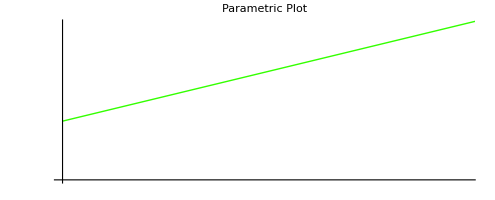

```mathematica
gr2=ParametricPlot[Evaluate[{H[t],P[t]}/.sol],{t,0,1000},PlotStyle->{Thick,Hue[0.3]},Ticks->{{{0.01,0},500,{500,"Host"},1000},{500,{500,"Parasite"},1000}},LabelStyle->{FontFamily->"Times",FontSize->16},PlotLabel->"Parametric Plot"]
```

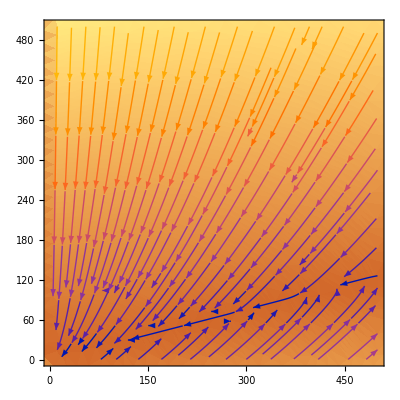

```mathematica
sp=StreamDensityPlot[{-H+ⅇ^(0.5000004588533404 (1-H/10000)-(2 ⅇ^(20/H) P)/(2+ⅇ^(20/H) H)) H,-P+0.5 H (1-(2 ⅇ^(20/H) P)/(2+ⅇ^(20/H) H))},{H,1,500},{P,1,500},StreamScale->Large]
```

```mathematica
Manipulate[StreamDensityPlot[{-H+ⅇ^(((rmax-rmin)/(1+ⅇ^(-beta (z-zbar)))+rmin) (1-H/k)-((z/(1+z)) Fmax P)/(Fmax+(z/(1+z)) H)) H,q H (1-((z/(1+z)) Fmax P)/(Fmax+(z/(1+z)) H))-P},{H,1,10000},{P,1,5000},StreamScale->Large],
{{rmax,2,"Max repro"},1,20,1},
{{rmin,0.5,"Min repro"},0,2,0.1},
{{beta,0.5,"beta"},0,1,0.1},
{{z,20,"Ind trait val"},0,100,10},
{{zbar,50,"chorus mean"},0,100, 10},
{{Fmax,2,"Max progeny"},0,5,1},
{{k,10000,"caryn cap"},10,100000,100},
{{q,1,"female prop"},0,2, 0.1}
]
```

```mathematica
host = (H* E^(((rmin + ((rmax -rmin)/(1 + E^(-beta * (z -zbar)))))* (1-(H/k)))-(((z/(1+z))*P*Fmax)/(Fmax +(z/(1+z))*H)))) - H
```

-H+ⅇ^((1-H/k) ((rmax-rmin)/(1+ⅇ^(-beta (z-zbar)))+rmin)-(Fmax P z)/((1+z) (Fmax+(H z)/(1+z)))) H

```mathematica
pars = ((H*(1-((z/(1+z))*P*Fmax)/(Fmax +(z/(1+z))*H))*q))-P
```

-P+H q (1-(Fmax P z)/((1+z) (Fmax+(H z)/(1+z))))

```mathematica
SS = Solve[host == 0 , H]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{H→0},{H→1/(2 (ⅇ^(beta (z-zbar)) rmax+rmin) z)(-ⅇ^(beta (z-zbar)) Fmax rmax-Fmax rmin-ⅇ^(beta (z-zbar)) Fmax rmax z+ⅇ^(beta (z-zbar)) k rmax z-Fmax rmin z+k rmin z-√(4 Fmax k (ⅇ^(beta (z-zbar)) rmax+rmin) z (ⅇ^(beta (z-zbar)) rmax+rmin-P z-ⅇ^(beta (z-zbar)) P z+ⅇ^(beta (z-zbar)) rmax z+rmin z)+(ⅇ^(beta (z-zbar)) Fmax rmax+Fmax rmin+ⅇ^(beta (z-zbar)) Fmax rmax z-ⅇ^(beta (z-zbar)) k rmax z+Fmax rmin z-k rmin z)^2))},{H→1/(2 (ⅇ^(beta (z-zbar)) rmax+rmin) z)(-ⅇ^(beta (z-zbar)) Fmax rmax-Fmax rmin-ⅇ^(beta (z-zbar)) Fmax rmax z+ⅇ^(beta (z-zbar)) k rmax z-Fmax rmin z+k rmin z+√(4 Fmax k (ⅇ^(beta (z-zbar)) rmax+rmin) z (ⅇ^(beta (z-zbar)) rmax+rmin-P z-ⅇ^(beta (z-zbar)) P z+ⅇ^(beta (z-zbar)) rmax z+rmin z)+(ⅇ^(beta (z-zbar)) Fmax rmax+Fmax rmin+ⅇ^(beta (z-zbar)) Fmax rmax z-ⅇ^(beta (z-zbar)) k rmax z+Fmax rmin z-k rmin z)^2))}}

```mathematica
SS2 = Solve[pars == 0 , P]
```

{{P→(H q (Fmax+Fmax z+H z))/(Fmax+Fmax z+H z+Fmax H q z)}}

```mathematica
jacobian = D[{host,pars},{{H,P}}]
```

{{-1+ⅇ^((1-H/k) ((rmax-rmin)/(1+ⅇ^(-beta (z-zbar)))+rmin)-(Fmax P z)/((1+z) (Fmax+(H z)/(1+z))))+ⅇ^((1-H/k) ((rmax-rmin)/(1+ⅇ^(-beta (z-zbar)))+rmin)-(Fmax P z)/((1+z) (Fmax+(H z)/(1+z)))) H (-((rmax-rmin)/(1+ⅇ^(-beta (z-zbar)))+rmin)/k+(Fmax P z^2)/((1+z)^2 (Fmax+(H z)/(1+z))^2)),-(ⅇ^((1-H/k) ((rmax-rmin)/(1+ⅇ^(-beta (z-zbar)))+rmin)-(Fmax P z)/((1+z) (Fmax+(H z)/(1+z)))) Fmax H z)/((1+z) (Fmax+(H z)/(1+z)))},{(Fmax H P q z^2)/((1+z)^2 (Fmax+(H z)/(1+z))^2)+q (1-(Fmax P z)/((1+z) (Fmax+(H z)/(1+z)))),-1-(Fmax H q z)/((1+z) (Fmax+(H z)/(1+z)))}}

```mathematica
J = MatrixForm[jacobian]/.{SS[[1]]}
```

```mathematica
{({{-1+ⅇ^((rmax-rmin)/(1+ⅇ^(-beta (z-zbar)))+rmin-(P z)/(1+z)), 0}, {q (1-(P z)/(1+z)), -1}})}
J2 = MatrixForm[jacobian]/.{SS2[[1]]}
```

{{{-1+ⅇ^((rmax-rmin)/(1+ⅇ^(-beta (z-zbar)))+rmin-(P z)/(1+z)),0},{q (1-(P z)/(1+z)),-1}}}

{(-1+ⅇ^((1-H/k) ((rmax-rmin)/(1+ⅇ^(-beta (z-zbar)))+rmin)-(Fmax H q z (Fmax+Fmax z+H z))/((1+z) (Fmax+Fmax z+H z+Fmax H q z) (Fmax+(H z)/(1+z))))+ⅇ^((1-H/k) ((rmax-rmin)/(1+ⅇ^(-beta (z-zbar)))+rmin)-(Fmax H q z (Fmax+Fmax z+H z))/((1+z) (Fmax+Fmax z+H z+Fmax H q z) (Fmax+(H z)/(1+z)))) H (-((rmax-rmin)/(1+ⅇ^(-beta (z-zbar)))+rmin)/k+(Fmax H q z^2 (Fmax+Fmax z+H z))/((1+z)^2 (Fmax+Fmax z+H z+Fmax H q z) (Fmax+(H z)/(1+z))^2)) | -(ⅇ^((1-H/k) ((rmax-rmin)/(1+ⅇ^(-beta (z-zbar)))+rmin)-(Fmax H q z (Fmax+Fmax z+H z))/((1+z) (Fmax+Fmax z+H z+Fmax H q z) (Fmax+(H z)/(1+z)))) Fmax H z)/((1+z) (Fmax+(H z)/(1+z)))
(Fmax H^2 q^2 z^2 (Fmax+Fmax z+H z))/((1+z)^2 (Fmax+Fmax z+H z+Fmax H q z) (Fmax+(H z)/(1+z))^2)+q (1-(Fmax H q z (Fmax+Fmax z+H z))/((1+z) (Fmax+Fmax z+H z+Fmax H q z) (Fmax+(H z)/(1+z)))) | -1-(Fmax H q z)/((1+z) (Fmax+(H z)/(1+z))))}

```mathematica
EV1 = Eigenvalues[J2/.{rmax ->2, rmin ->1,beta -> 1, k -> 10000, Fmax -> 2, q -> 0.1, z-> 20, zbar ->50, P -> 50, H->500}]
```

Eigenvalues[{(1.44274 | -4.36174
0.0999305 | -1.19916)}]

```mathematica
REV = N[Re[EV1]]
```

Re[Eigenvalues[{(1.44274 | -4.36174
0.0999305 | -1.19916)}]]

```mathematica
IEV = N[Im[EV1]]
```

Im[Eigenvalues[{(1.44274 | -4.36174
0.0999305 | -1.19916)}]]

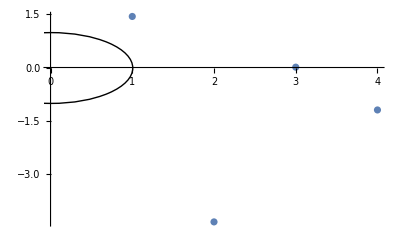

```mathematica
Show[{ListPlot[{1.442, -4.361, 0.0099, -1.199}]}, {Graphics[Circle[]]}]
```